## Introduction

First, a little bit of terminology:
- simulation: data of a simulation.full.json file, generated by the pipeline;
- result: data of a result.csv file, containing additional informations about a series of simulations (most importantly, the road curvature data);
- simres: association of a simulation (under the simulation key) and a result row (under the result key);
- dataset: list of elements of the form {N curvature values} -> {N oob_distance values}.

## BeamNG Simulation data

### Importing simulations

```mathematica
ToAbsolutePath[path_,absolute_:False]:=If[absolute,path,FileNameJoin[{NotebookDirectory[],path}]];
```

```mathematica
(* Import a single simulation JSON file (via relative path). Returns an association. *)
ImportSimulation[path_,absolute_:False]:=Module[{ap,simulation},
simulation=Import[ToAbsolutePath[path,absolute], "RawJSON"];
simulation[["road","nodes"]]=simulation[["road","nodes",All,{1,2}]];
simulation[["records"]]=MapAt[#[[1;;2]]&,simulation[["records"]],{All,"pos"}];
simulation
]
```

```mathematica
(* Some information about the schema *)
simulation=ImportSimulation["simulation.full.json"];
simulation[["params"]]//Keys
simulation[["info"]]//Keys
simulation[["road"]]//Keys
simulation[["records"]]//First//Keys
```

{beamng_steps,delay_msec}

{id,success,start_time,computer_name,end_time}

{name,nodes}

{timer,pos,dir,vel,steering,steering_input,brake,brake_input,throttle,throttle_input,wheelspeed,vel_kmh,is_oob,oob_counter,max_oob_percentage,oob_distance}

```mathematica
(* Imports all the simulations in the ../results folder. Returns a list of simulations *)
ImportSimulationFolder[path_:"../results",absolute_:False]:=Module[{ps},
ps=FileNames["simulation.full.json",ToAbsolutePath[path,absolute],2];
ImportSimulation[#,True]&/@ps
]
```

### Convenience functions

```mathematica
RoadNodes[simulation_]:=simulation[["road","nodes",All]]
CarPositions[simulation_]:=simulation[["records",All,"pos"]]
```

### Timestamped scalar data

```mathematica
CarRecord[simulation_,name_]:=simulation[["records", All, name]]
TimestampedCarRecord[simulation_,key_]:=Values/@simulation[["records", All, {"timer",key}]]
(* Add timestamp to a list of values
	{1, 2, 3, ...} -> {{0, 1}, {0.1, 2}, {0.4, 3}, ...}
 *)
Timestamped[simulation_,list_]:=Transpose[{simulation[["records", All, "timer"]][[;;Length[list]]],list}]
```

### Visualization functions

```mathematica
(* Plots the road and the car trajectory. The black dot symbolizes the initial position of the car. *)
PlotCarTrajectory[simulation_]:=Show[
ListLinePlot[{
Legended[RoadNodes[simulation],"Road"],
Legended[CarPositions[simulation],"Car"]
}],
Graphics[{PointSize[Large],Point[First[CarPositions[simulation]]]},ImageSize->Large]
]
```

```mathematica
PlotCarDeviation[simulation_]:=Module[{minDistanceToRoad,velocity},
minDistanceToRoad=Timestamped[
simulation,
Map[
Function[p,Min[EuclideanDistance[p,#]&/@RoadNodes[s]]],
CarPositions[s]
]
];
velocity=Timestamped[simulation,Norm/@CarRecord[s,"vel"]];
ListLinePlot[{
Labeled[TimestampedCarRecord[simulation,"oob_distance"],"oob_distance"],
Labeled[minDistanceToRoad,"Distance to road center"],
Labeled[velocity,"Velocity"]
},ImageSize->Large]
]
```

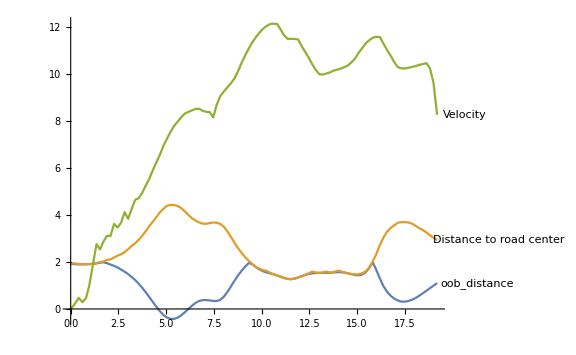

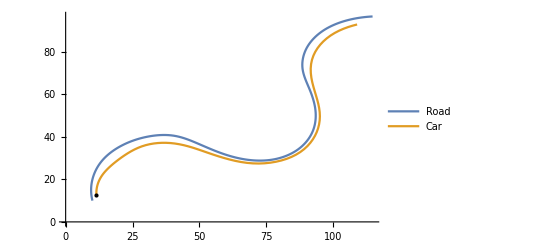

```mathematica
PlotCarDeviation[simulation]
PlotCarTrajectory[simulation]
```

## CSV results

### Importing

```mathematica
(* Imports a CSV point list e.g. "[(1, 2), (3, 4)]" *)
ImportCSVPointList[string_]:=Module[{points},
points=StringTake[string,{3,-3}];
points=StringSplit[points,"), ("];
points=StringSplit[#,", "]&/@points;
MapAt[ImportString[#,"JSON"]&,points,{All,All}]
]

(* Imports a CSV result file. Automatically drops rows corresponding to invalid roads. *)
ImportResults[path_,absolute_:False]:=Module[{raw,result},
raw=Normal[Import[ToAbsolutePath[path,absolute], "Dataset","HeaderLines"->1]];
raw=DeleteCases[raw,a_/;Length[a]==0||a[["outcome"]]=="INVALID"];
Table[
result=raw[[i]];
AssociateTo[result,"kappas"->If[StringLength[result[["kappas"]]]>0,ImportString[result[["kappas"]],"JSON"],{}]];
AssociateTo[result,"road"->If[StringLength[result[["road"]]]>0,ImportCSVPointList[result[["road"]]],{}]];
result,
{i,1,Length[raw]}
]
]
```

```mathematica
results=ImportResults["results.csv"];
results[[1]]//Keys
```

{,description,kappas,method,outcome,road,accum_neg_oob,avg_brake,avg_brake_input,avg_oob_counter,avg_oob_distance,avg_steering,avg_steering_input,avg_throttle,avg_throttle_input,avg_vel_kmh,avg_wheelspeed,max_brake,max_brake_input,max_oob_counter,max_oob_distance,max_oob_percentage,max_steering,max_steering_input,max_throttle,max_throttle_input,max_vel_kmh,max_wheelspeed,mean_brake,mean_brake_input,mean_oob_counter,mean_oob_distance,mean_steering,mean_steering_input,mean_throttle,mean_throttle_input,mean_vel_kmh,mean_wheelspeed,min_brake,min_brake_input,min_oob_counter,min_oob_distance,min_steering,min_steering_input,min_throttle,min_throttle_input,min_vel_kmh,min_wheelspeed,parent_index,parent_min_oob_distance,parent_outcome}

-Graphics-

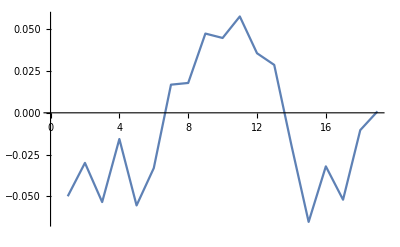

```mathematica
PlotCarTrajectory[simulation]
ListLinePlot[results[[1,"kappas"]]]
```

### Convenience functions

```mathematica
RoadKappas[result_]:=result[["kappas"]]
```

## Full directory import

```mathematica
(* Prints basic informations about a collection of simulations *)
PrintBasicInformations[simresList_,title_:"",importTime_:0]:=Print[
TableForm[
{
If[title≠"",{"","----- "<>title<>" -----"}],
If[importTime≠0,{"Import time",importTime}],
{"Count", Length[simresList]},
{"Successful",Count[simresList,d_/;d[["result","outcome"]]=="PASS"]},
{"Failed",Count[simresList,d_/;d[["result","outcome"]]≠"PASS"]}
}
]]
```

```mathematica
ImportFolder[path_,absolute_:False]:=Module[{p,t,ss,rs,rn,ds},
p=ToAbsolutePath[path,absolute];
rn=First[FileNames["*.csv",p,1]];
t=Timing[
rs=ImportResults[rn,True];
ss=ImportSimulationFolder[p,True];
ds=Map[AssociationThread[{"simulation","result"},#]&,Transpose[{ss, rs}]];
ds=DeleteCases[ds,d_/;Length[d[["result","kappas"]]]==0];
];
PrintBasicInformations[ds,p,First[t]];
ds
]
```

```mathematica
data=ImportFolder["1"];
```

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/1 -----
Import time | 0.938621
Count | 3
Successful | 3
Failed | 0

```mathematica
PlotCarTrajectoryWithCurvature[simres_]:=Module[{plot,rcp,ccp,cplot},
plot=PlotCarTrajectory[simres[["simulation"]]];
rcp=Transpose[{simres[["result","road"]],simres[["result","kappas"]]}];
ccp=MapAt[First@Nearest[CarPositions[simres[["simulation"]]],#]&,rcp,{All,1}];
cplot=ListPlot[{
Labeled[#[[1]],SetPrecision[#[[2]],1]]&/@rcp,
First/@ccp
}];
Show[plot,cplot]
]
```

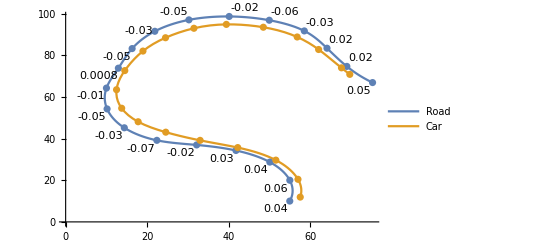

```mathematica
PlotCarTrajectoryWithCurvature[data[[3]]]
```

```mathematica
(* Returns the car records which are closest to a roat point with specified curvature. Enriches the records with these curvature values. *)
CarRecordsWithCurvature[simres_]:=Module[{tp,pc,ra},
pc=Transpose[{simres[["result","road"]],simres[["result","kappas"]]}];
pc=MapAt[First@Nearest[CarPositions[simres[["simulation"]]],#]&,pc,{All,1}];
pc=AssociationThread[{"pos","kappa"},#]&/@pc;
JoinAcross[simres[["simulation","records"]],pc,Key["pos"]]
]
```

```mathematica
PlotOobToCurvature[simres_,curvatureFactor_:1]:=Module[{rs,oobp,cp},
rs=CarRecordsWithCurvature[simres];
oobp=Values[rs[[All,{"timer","oob_distance"}]]];
cp=Values[rs[[All,{"timer","kappa"}]]];
ListLinePlot[{
Legended[oobp,"oob_distance"],
Legended[MapAt[curvatureFactor*#&,cp,{All,2}],"Curvature * "<>ToString[curvatureFactor]]
},Filling->{1->{2}},PlotLabel->"Correlation: " <>ToString[Correlation[oobp[[All,2]],cp[[All,2]]]]]
]
```

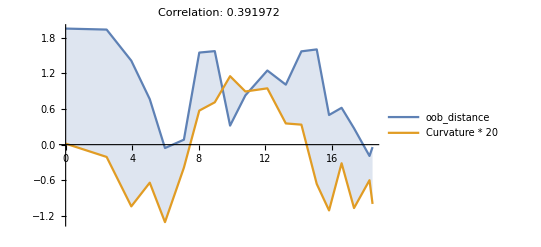

```mathematica
PlotOobToCurvature[data[[2]],20]
```

## Data consolidation

```mathematica
(* Import multiple folders at once. Returns a list of simres *)
ImportFolders[paths_,absolute_:False]:=Module[{ds,t},
t=Timing[
ds=Catenate[ImportFolder[#,absolute]&/@paths];
];
PrintBasicInformations[ds,"TOTAL",First[t]];
ds
]
```

```mathematica
ImportDump[path_,absolute_:False]:=Module[{ds,t,p},
p=ToAbsolutePath[path,absolute];
t=Timing[ds=Import[ToAbsolutePath[path,absolute],"RawJSON"];];
Print[TableForm[{
{"Source", p},
{"Simulation count",Length[ds]},
{"Import time",First[t]}
}]];
ds
]
ExportDump[simresList_,path_,absolute_:False]:=Module[{t,p},
p=ToAbsolutePath[path,absolute];
t=Timing[Export[p,simresList,"RawJSON"]];
Print[TableForm[{
{"Destination", p},
{"Simulation count",Length[simresList]},
{"Export time",First[t]}
}]];
]
```

```mathematica
data=ImportFolders[{"1","2","3","4"}];
ExportDump[data,"1-4.dat"];
```

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/1 -----
Import time | 0.503075
Count | 3
Successful | 3
Failed | 0

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/2 -----
Import time | 7.04214
Count | 188
Successful | 177
Failed | 11

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/3 -----
Import time | 6.54509
Count | 191
Successful | 176
Failed | 15

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/4 -----
Import time | 12.4176
Count | 337
Successful | 319
Failed | 18

| ----- TOTAL -----
Import time | 26.5875
Count | 719
Successful | 675
Failed | 44

Destination | /Users/cedric/repositories/sbst-tool-competition-av/rd/1-4.dat
Simulation count | 719
Export time | 1.93509

```mathematica
data=ImportDump["1-4.dat"];
```

Source | /Users/cedric/repositories/sbst-tool-competition-av/rd/1-4.dat
Simulation count | 719
Import time | 2.28517

## Machine leaning experiments

### Data import

```mathematica
data=ImportDump["1-4.dat"];
```

Source | /Users/cedric/repositories/sbst-tool-competition-av/rd/1-4.dat
Simulation count | 719
Import time | 2.2636

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

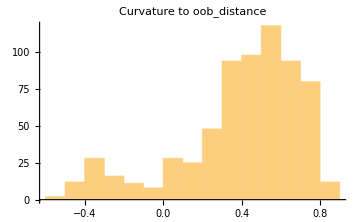
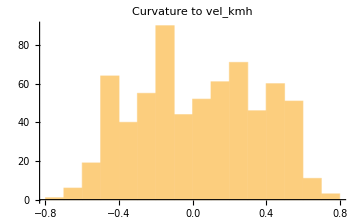
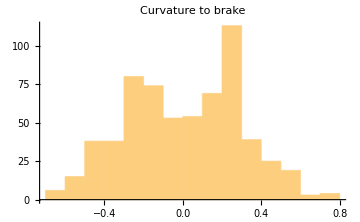

```mathematica
Table[
Histogram[
Correlation[#[[All,metric]],#[[All,"kappa"]]]&/@
(CarRecordsWithCurvature/@Cases[data,d_/;d[["result","outcome"]]=="PASS"]),
PlotLabel->"Curvature to "<>metric,ImageSize->Medium],
{metric,{"oob_distance","vel_kmh","brake"}}
]//Row
```

```mathematica
(* Creates a dataset, which is a list whose items are of the form
  {N kappa values} -> {N oob_distance values}
   WARNING: THIS MAY BE THE OPPOSITE OF WHAT YOU NEED. 
Use Reverse[dataset, {2}] to create the serverse set.
 *)
ToDataset[simresList_,shuffle_:False]:=Map[
Function[d,
r=CarRecordsWithCurvature[d];
r[[All,"kappa"]]->Abs[r[[All,"oob_distance"]]]
],
If[shuffle,RandomSample,Identity][simresList]
];
```

```mathematica
(* Splits a list into a training set (trainingPercentage_ % of the whose set) and a validation set *)
SplitDataset[list_,trainingPercentage_:0.8]:=Module[{i},
i=Floor[Length[list]*trainingPercentage]; 
{list[[;;i]],list[[i+1;;]]}
]
```

```mathematica
(* Computes the loss of a predictor on a single example *)
Loss[predictor_,example_]:=MeanAbsoluteLossLayer[][<|"Input"->predictor[example[[1]]],"Target"->example[[2]]|>];
AverageLoss[predictor_,validationSet_]:=Mean[Loss[predictor,#]&/@validationSet];
```

```mathematica
(* Plots a histogram representing the accuracy if a predictor against a validation set. *)
PlotLoss[predictor_,validationSet_]:=Module[{losses},
losses=Loss[predictor,#]&/@validationSet;
Histogram[losses,PlotLabel->"Average loss: "<>ToString[Mean[losses]],ImageSize->Medium]
]
```

```mathematica
VizualizePredictions[predictor_,dataSet_]:=Manipulate[
ListLinePlot[{
Legended[dataSet[[j,2]],"Real curvature"],
Legended[predictor[dataSet[[j,1]]],"Predicted curvature"]
},ImageSize->Large,Filling->{2->{1}},PlotLabel->"Loss: "<>ToString[Loss[predictor,dataSet[[j]]]]
],
{j,1,Length[dataSet],1}
]
```

### Dimension reduction

```mathematica
passDataset=Reverse[ToDataset[Cases[data,d_/;d[["result","outcome"]]=="PASS"]],{2}];
failDataset=Reverse[ToDataset[Cases[data,d_/;d[["result","outcome"]]!="PASS"]],{2}];
```

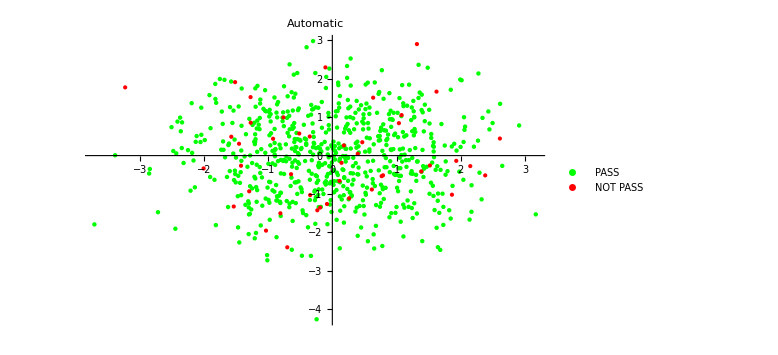
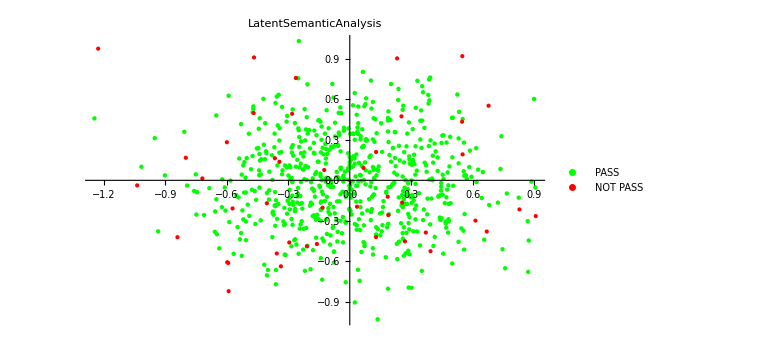
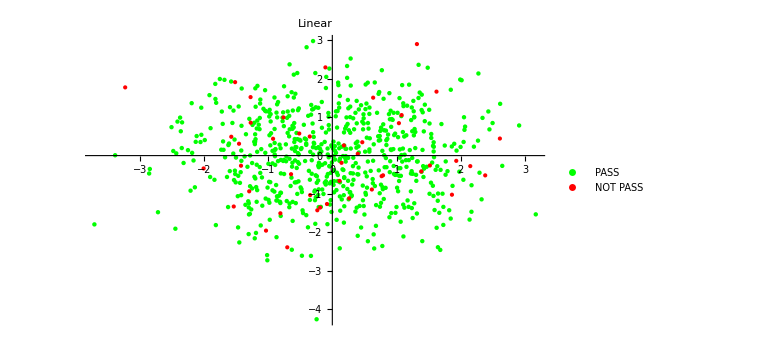
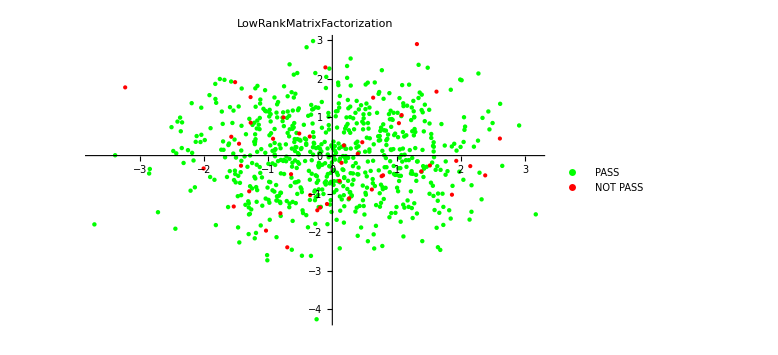
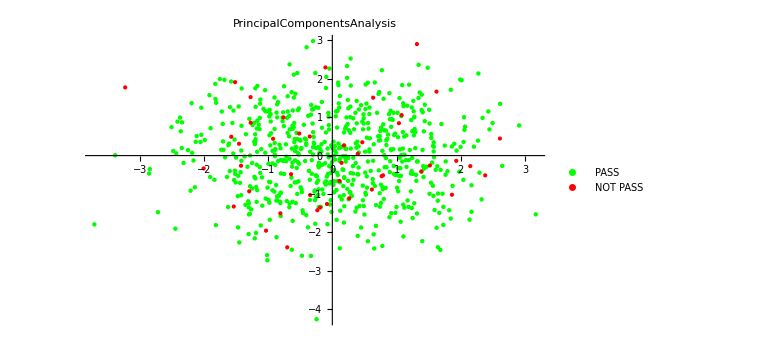
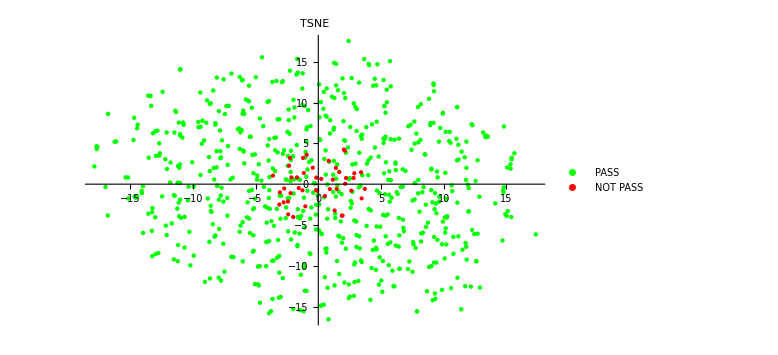
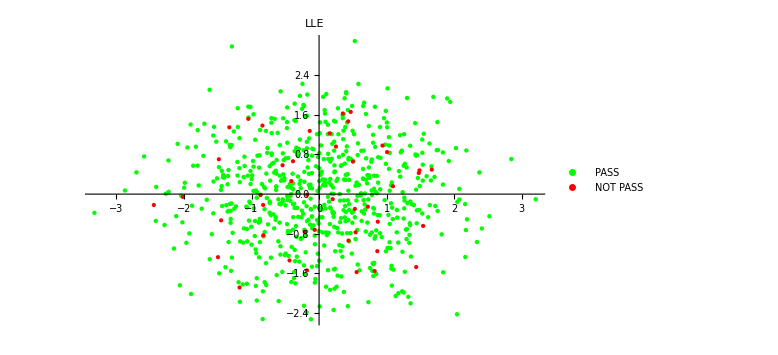
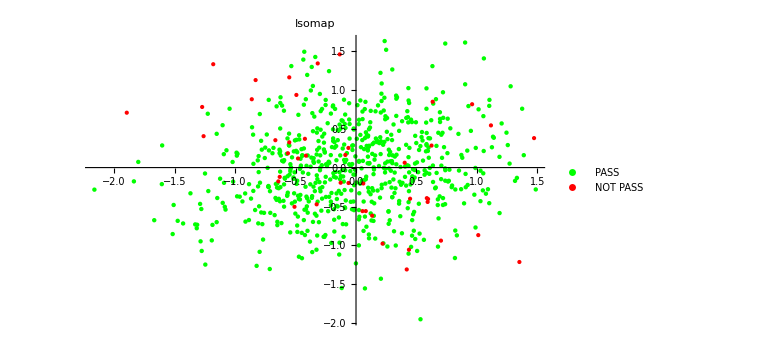

```mathematica
methods={Automatic,"LatentSemanticAnalysis","Linear","LowRankMatrixFactorization","PrincipalComponentsAnalysis","TSNE","LLE","Isomap"};
Table[
ListPlot[{
Legended[DimensionReduce[passDataset,Method->m],"PASS"],
Legended[DimensionReduce[failDataset,Method->m],"NOT PASS"]
},PlotLabel->m,ImageSize->Large,PlotStyle->{Green,{Red,PointSize[Large]}}],
{m,methods}
]//Column
```

```mathematica
Table[
ListPointPlot3D[{
Legended[DimensionReduce[passDataset,3,Method->m],"PASS"],
Legended[DimensionReduce[failDataset,3,Method->m],"NOT PASS"]
},PlotLabel->m,ImageSize->Large,PlotStyle->{Green,{Red,PointSize[Large]}}],
{m,methods}
]//Column
```

-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-
-Graphics3D-

### Predicting |min_oob_distance|

```mathematica
dataset=#[["result","kappas"]]->Abs[#[["result","min_oob_distance"]]]&/@data;
{trainingDataset,validationDataset}=SplitDataset[RandomSample[dataset],0.8];
```

```mathematica
methods={"DecisionTree","GradientBoostedTrees","LinearRegression","NearestNeighbors","NeuralNetwork","RandomForest","GaussianProcess"};
predictors=AssociationMap[Predict[trainingDataset,Method->#]&,methods];
```

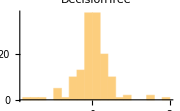
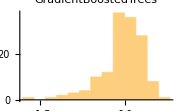
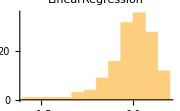
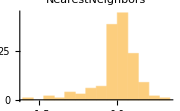
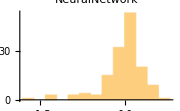
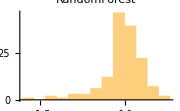
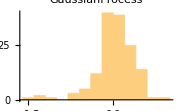

```mathematica
KeyValueMap[
Function[
{m,p},
Histogram[p[#[[1]]]-#[[2]]&/@validationDataset,PlotLabel->m,ImageSize->Small]
],
predictors
]//Row
```

### Predicting the car trajectory

Here, we are predicting all 19 oob_distance values separately

```mathematica
data//First//CarRecordsWithCurvature//Length
```

19

```mathematica
{trainingDataset,validationDataset}=SplitDataset[ToDataset[data,True],0.9];
```

```mathematica
predictors=ParallelTable[
Predict[#[[1]]->#[[2,i]]&/@trainingDataset,Method->"DecisionTree",TrainingProgressReporting->None],
{i,1,19}
];
predictor=Function[ks,Table[p[ks],{p,predictors}]];
```

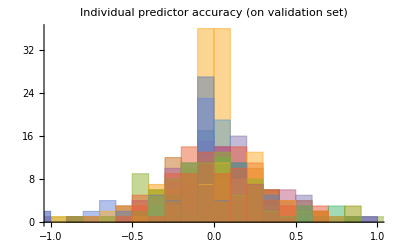

```mathematica
Histogram[Table[
predictors[[i]][#[[1]]]-#[[2,i]]&/@validationDataset,
{i,1,19}
],PlotLabel->"Individual predictor accuracy (on validation set)"]
```

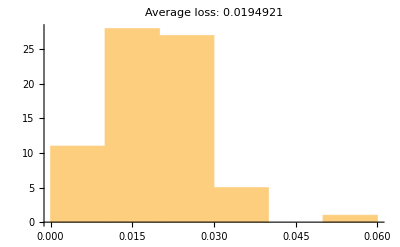

```mathematica
PlotLoss[predictor,validationDataset]
```

```mathematica
VizualizePredictions[predictor,validationDataset]
```

### Predicting the curvature

```mathematica
{trainingDataset,validationDataset}=SplitDataset[Reverse[ToDataset[data,True],{2}],0.9];
```

The predictors are expected to predict a curvature value given the oob_distance’s values of the car

```mathematica
predictors=ParallelTable[
Predict[#[[1]]->#[[2,i]]&/@trainingDataset,Method->"DecisionTree",TrainingProgressReporting->None],
{i,1,19}
];
predictor=Function[ks,Table[p[ks],{p,predictors}]];
```

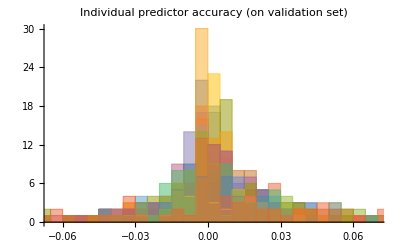

```mathematica
Histogram[Table[
predictors[[i]][#[[1]]]-#[[2,i]]&/@validationDataset,
{i,1,19}
],PlotLabel->"Individual predictor accuracy (on validation set)"]
```

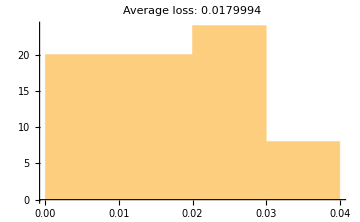

```mathematica
PlotLoss[predictor,validationDataset]
```

```mathematica
VizualizePredictions[predictor,validationDataset]
```

How fast does this method reach satisfactory accuracy: (disclaimer: the x axis values aren’t actually meaningful)

ParallelTable::subpar: -- Message text not found --

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: -- Message text not found --

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: -- Message text not found --

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

ParallelTable::subpar: -- Message text not found --

General::stop: Further output of ParallelTable::subpar will be suppressed during this calculation.

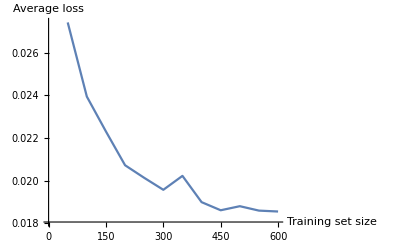

```mathematica
ListLinePlot[
ParallelTable[
predictors=ParallelTable[
Predict[#[[1]]->#[[2,i]]&/@trainingDataset[[;;j]],Method->"DecisionTree",TrainingProgressReporting->None],
{i,1,19}
];
predictor=Function[ks,Table[p[ks],{p,predictors}]];
{j,Mean[Loss[predictor,#]&/@validationDataset]},
{j,50,600,50}
],
AxesLabel->{"Training set size","Average loss"}
]
```

### Neural networks

```mathematica
MakeInitializedNetwork[layerSizes_]:=NetInitialize@NetChain[LinearLayer/@Join[layerSizes,{19}],"Input"->19,"Output"->19];
MakeTrainingNetwork[initializedNetwork_]:=NetGraph[
<|"network"->initializedNetwork,"loss"->MeanAbsoluteLossLayer["Input"->19]|>,
{NetPort["Input"]->"network"->NetPort["loss","Input"],NetPort["Target"]->NetPort["loss","Target"]}
];
```

```mathematica
{trainingDataset,validationDataset}=SplitDataset[Reverse[ToDataset[data,True],{2}],0.9];
```

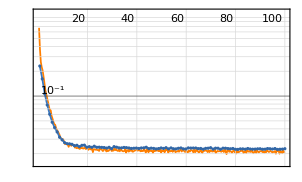
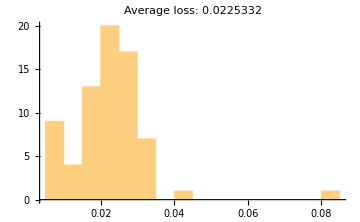
NetTrain Results
summary | ,,  batches:1100  rounds:100  time:0.87s  examples/s:81031
data | ,,  training examples:647  validation examples:72  processed examples:70400  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.11×10^-2
validation | ,,  loss:2.3×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | -Graphics-

```mathematica
initializedNetwork=MakeInitializedNetwork[{50,20,100}];
trainingNetwork=MakeTrainingNetwork[initializedNetwork];
results=NetTrain[trainingNetwork,trainingDataset,All,MaxTrainingRounds->100,ValidationSet->validationDataset];
trainedNetwork=NetExtract[results["TrainedNet"],"network"];
Row[{results,PlotLoss[trainedNetwork,validationDataset]}]
```

Convergence speed

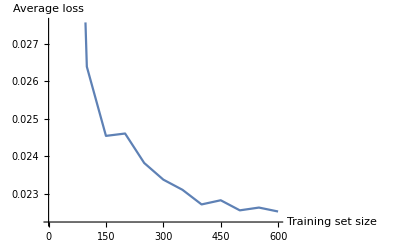

```mathematica
initializedNetwork=MakeInitializedNetwork[{50,20,100}];
trainingNetwork=MakeTrainingNetwork[initializedNetwork];
ListLinePlot[
Table[
tn=NetTrain[trainingNetwork,trainingDataset[[;;j]],"TrainedNet",
MaxTrainingRounds->100,TrainingProgressReporting->None,ValidationSet->validationDataset];
n=NetExtract[tn,"network"];
{j,AverageLoss[n,validationDataset]},
{j,50,600,50}
],
AxesLabel->{"Training set size","Average loss"}
]
```

### Finding “fastest” network layout (don’t run these unless you want your laptop to go to space)

The goal is to find the layout that converges the fastest, i.e. that is the most accurate being trained on 200 examples. This is not the same as searching for the network that is eventually the most accurate.

#### 2 layers

```mathematica
(* To plot losses, you need to flatten it by (nb. of parameters - 1) *)
losses2d=ParallelTable[
t=MakeTrainingNetwork[MakeInitializedNetwork[{l1,l2}]];
tn=NetTrain[t,trainingDataset[[;;200]],"TrainedNet",MaxTrainingRounds->100,ValidationSet->validationDataset,TrainingProgressReporting->None];
n=NetExtract[tn,"network"];
{l1,l2,AverageLoss[n,validationDataset]},
{l1,20,100,10},
{l2,20,100,10}
];
```

```mathematica
SortBy[Flatten[losses2d,1],Last][[;;10]]//TableForm
```

60 | 90 | 0.0233148
50 | 100 | 0.0233532
70 | 100 | 0.0234658
100 | 80 | 0.023531
90 | 80 | 0.0235816
60 | 40 | 0.0235848
70 | 50 | 0.0235856
60 | 50 | 0.0236249
40 | 70 | 0.0236558
90 | 40 | 0.0237055

#### 3 layers

```mathematica
losses3d=ParallelTable[
t=MakeTrainingNetwork[MakeInitializedNetwork[{l1,l2,l3}]];
tn=NetTrain[t,trainingDataset[[;;200]],"TrainedNet",MaxTrainingRounds->100,ValidationSet->validationDataset,TrainingProgressReporting->None];
n=NetExtract[tn,"network"];
{l1,l2,l3,AverageLoss[n,validationDataset]},
{l1,20,100,10},
{l2,20,40,10},
{l3,20,100,10}
];
```

```mathematica
SortBy[Flatten[losses3d,2],Last][[;;10]]//TableForm
```

50 | 20 | 100 | 0.0224015
80 | 20 | 80 | 0.0224226
100 | 20 | 80 | 0.0225269
50 | 20 | 80 | 0.0225296
80 | 30 | 100 | 0.0225448
60 | 20 | 90 | 0.0225629
80 | 20 | 90 | 0.0226206
100 | 20 | 100 | 0.0226891
60 | 20 | 60 | 0.0226984
80 | 20 | 50 | 0.022711

#### 4 layers

Based on the results of the 3 layer search, we allow very little leeway on the first 3 layers

```mathematica
losses4d=ParallelTable[
t=MakeTrainingNetwork[MakeInitializedNetwork[{l1,l2,l3,l4}]];
tn=NetTrain[t,trainingDataset[[;;200]],"TrainedNet",MaxTrainingRounds->100,ValidationSet->validationDataset,TrainingProgressReporting->None];
n=NetExtract[tn,"network"];
{l1,l2,l3,l4,AverageLoss[n,validationDataset]},
{l1,20,140,10},
{l2,20,50,10},
{l3,20,50,10},
{l4,20,100,10}
];
```

```mathematica
SortBy[Flatten[losses4d,3],Last][[;;10]]//TableForm
```